```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]<>"\\Code\\OutputData"];
```

```mathematica
(*Проверим консвервативность схемы для различных σ*)
```

```mathematica
(*σ=0.*)
points1=Import["test4-sigma0","Table", PerformanceGoal->"Speed"];
```

```mathematica
(*σ=0.5*)
points2=Import["test4-sigma05","Table", PerformanceGoal->"Speed"];
```

```mathematica
(*σ=1.*)
points3=Import["test4-sigma1","Table", PerformanceGoal->"Speed"];
```

```mathematica
h = 0.005; 
τ=0.0002;
consDiff[statecur_, statenext_]:=Abs[h/2 statenext[[2]] + h *Sum[statenext[[k]],{k,3,Length[statenext]-1}]+h/2*statenext[[Length[statenext]]]-(h/2 statecur[[2]] + h *Sum[statecur[[i]],{i,3,Length[statecur]-1}]+h/2*statecur[[Length[statecur]]])];
```

```mathematica
consDiff[points3[[2]],points3[[3]]]
```

1.13687×10^-13

```mathematica
conserv1 = Table[{τ*i, consDiff[points1[[i]],points1[[i+1]]]},{i,1,Length[points1]-1 }];
```

```mathematica
conserv2 = Table[{τ*i, consDiff[points2[[i]],points2[[i+1]]]},{i,1,Length[points2]-1 }];
```

```mathematica
conserv3 = Table[{τ*i, consDiff[points3[[i]],points3[[i+1]]]},{i,1,Length[points3]-1 }];
```

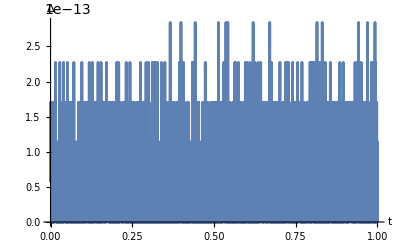

```mathematica
ListPlot[conserv1, PerformanceGoal->"Speed", Joined->True, AxesLabel->{"t", "Δ"}]
```

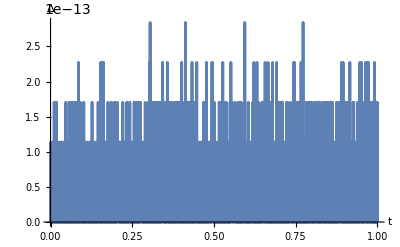

```mathematica
ListPlot[conserv2, PerformanceGoal->"Speed", Joined->True, AxesLabel->{"t", "Δ"}]
```

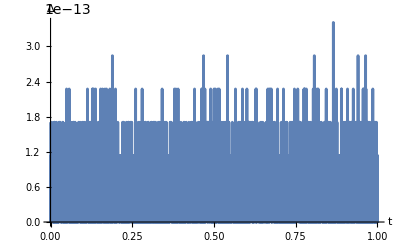

```mathematica
ListPlot[conserv3, PerformanceGoal->"Speed", Joined->True, AxesLabel->{"t", "Δ"}]
```